```mathematica
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]];
If[!MemberQ[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]],AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]]];
Print["Package path ",FindFile["GDCComparisons`"]];
Print["Package path ",FindFile["GDCAnalysis3`"]];
<<GDCComparisons`
<<GDCAnalysis3`
```

Package path /home/carla/GDC/DialecticalStructures/GDCComparisons.m

Package path /home/carla/GDC/DialecticalStructures/GDCAnalysis3.m

```mathematica
filesAR=FileNames["/home/carla/GDC/CH_Pool/DLB/GDC_CHP_AR_DLB_ALL_Out/*.txt"];
inputAR=Map[Get[#]&, filesAR];
dojAR=inputAR[[All,1]];
zAR=inputAR[[All,2]];
fAR=inputAR[[All,3]];
filesBR=FileNames["/home/carla/GDC/CH_Pool/DLB/GDC_CHP_BR_DLB_ALL_Out/*.txt"];
inputBR=Map[Get[#]&, filesBR];
dojBR=inputBR[[All,1]];
zBR=inputBR[[All,2]];
fBR=inputBR[[All,3]];
```

```mathematica
(*MIN Values*)
Map[dojBR[[#]][[1]][["value"]]&,Range[Length[fBR]]]
Map[zBR[[#]][[1]][["value"]]&,Range[Length[fBR]]]
Map[fBR[[#]][[1]][["value"]]&,Range[Length[fBR]]]
```

{0.,0.,0.,0.,0.,0.,0.,0.}

{-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.}

{-1,-1,-1,-1,-1,-1,-1,-1}

```mathematica
tsAR={0,1,2,3,4,5,6,7,8};
tsBR={0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5};
tsAll=Union[tsAR,tsBR];
```

```mathematica
dojMax=maxValFunc[tsAR, tsBR, dojAR, dojBR, "DLB", "DOJ"]
zMax=maxValFunc[tsAR, tsBR, zAR, zBR, "DLB", "Z"]
fMax=maxValFunc[tsAR, tsBR, fAR, fBR, "DLB", "F"]
```

{{0,1.},{0.5,1.},{1,1.},{1.5,1.},{2,0.00146843},{2.5,0.00146843},{3,0.00645161},{3.5,0.00645161},{4,0.00746269},{4.5,0.0119336},{5,0.00613497},{5.5,0.00452489},{6,0.028169},{6.5,0.00816327},{7,0.0344828},{7.5,0.0344828},{8,1.}}

{{0,1.},{0.5,1.},{1,1.},{1.5,1.},{2,0.00119082},{2.5,0.00120299},{3,0.0061875},{3.5,0.00617399},{4,0.00718535},{4.5,0.0104023},{5,0.00592072},{5.5,0.0043884},{6,0.0273123},{6.5,0.00728468},{7,0.0336275},{7.5,0.0336245},{8,1.}}

{{0,1},{0.5,1},{1,1},{1.5,1},{2,0.682016},{2.5,0.69382},{3,0.921345},{3.5,0.917488},{4,0.928336},{4.5,0.934124},{5,0.932512},{5.5,0.94144},{6,0.970326},{6.5,0.899077},{7,0.951595},{7.5,0.951432},{8,1}}

```mathematica
dojTat=Get["/home/carla/GDC/CONF/DLB/DLB_DOJ.txt"]
zTat=Get["/home/carla/GDC/CONF/DLB/DLB_Z.txt"]
fTat=Get["/home/carla/GDC/CONF/DLB/DLB_F.txt"]
```

{{0,1.},{0.5,1.},{1,1.},{1.5,1.},{2,0.00146843},{2.5,0.00146843},{3,0.00645161},{3.5,0.00645161},{4,0.00746269},{4.5,0.00628931},{5,0.00613497},{5.5,0.00452489},{6,0.028169},{6.5,0.00816327},{7,0.0344828},{7.5,0.0344828},{8,1.}}

{{0,1.},{0.5,1.},{1,1.},{1.5,1.},{2,0.00119082},{2.5,0.00120299},{3,0.0061875},{3.5,0.00617399},{4,0.00703189},{4.5,0.00596426},{5,0.00580987},{5.5,0.00431789},{6,0.0273054},{6.5,0.00727735},{7,0.0336203},{7.5,0.0336171},{8,1.}}

{{0,1},{0.5,1},{1,1},{1.5,1},{2,0.682016},{2.5,0.69382},{3,0.921345},{3.5,0.917488},{4,0.890847},{4.5,0.901714},{5,0.899351},{5.5,0.912511},{6,0.940507},{6.5,0.804199},{7,0.951201},{7.5,0.951024},{8,1}}

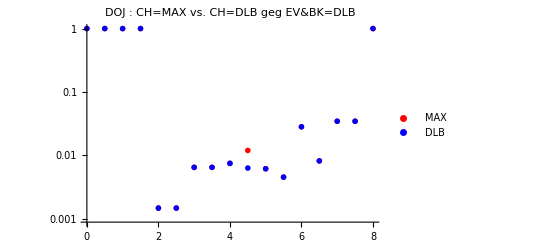
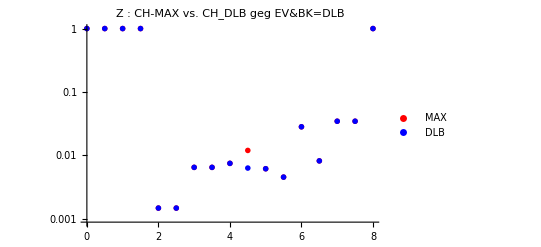
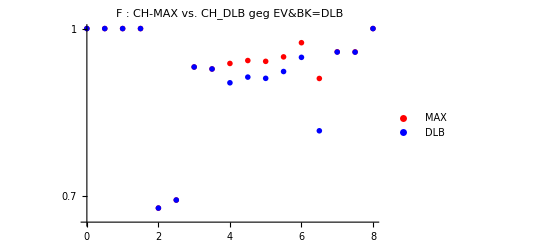

```mathematica
dojPlot=ListLogPlot[{dojMax,dojTat},PlotLegends->{"MAX", "DLB"},PlotStyle->{Red, Blue},PlotLabel->"DOJ : CH=MAX vs. CH=DLB geg EV&BK=DLB",PlotMarkers->{{"X",12}, {"D",12}}, ImageSize->400];
zPlot=ListLogPlot[{dojMax,dojTat},PlotLegends->{"MAX", "DLB"},PlotStyle->{Red, Blue},PlotLabel->"Z : CH-MAX vs. CH_DLB geg EV&BK=DLB",PlotMarkers->{{"X",12}, {"D",12}}, ImageSize->400];
fPlot=ListLogPlot[{fMax,fTat},PlotLegends->{"MAX", "DLB"},PlotStyle->{Red, Blue},PlotLabel->"F : CH-MAX vs. CH_DLB geg EV&BK=DLB",PlotMarkers->{{"X",12}, {"D",12}}, ImageSize->400];
confMAX=Column[{dojPlot,zPlot,fPlot}]
```

```mathematica
(* Früher DOJ CH-MAX>CH-DLB für {4.5, 5, 5.5} 
Jetzt DOJ CH-MAX>CH-DLB für {4.5} 
WARUM?????? 
dojBR[[5,2]][["value"]]
dojTat[[10]]
dojBR[[5,2]][["list"]][[1;;3]]*)
```

```mathematica
tatCH=Map[Get[#]&,FileNames["/home/carla/GDC/POS/*.txt"]];
persInd=First[persMixFunc["DLB"]];
```

```mathematica
Map[compCHMaxFunc[persInd, #, tatCH , dojBR]&,{4.5}]
```

{{0.466667,0.533333,0.4,0.466667,0.6,0.533333,0.533333,0.4,0.466667,0.6,0.533333,0.6,0.666667,0.533333,0.6,0.6,0.666667,0.533333,0.6,0.466667,0.533333,0.533333,0.6,0.466667,0.533333,0.533333,0.6,0.466667,0.533333}}

```mathematica
Map[vvPosFunc[persInd,# , tatCH, "CH", "PEN"]&,{4.5}]
Map[vvPosFunc[persInd,# , dojBR,  "CH", "PEN"]&,{4.5}]
```

{0.533333}

{{0.8,0.733333,0.733333,0.666667,0.666667,0.6,0.866667,0.866667,0.8,0.8,0.733333,0.666667,0.6,0.733333,0.666667,0.666667,0.6,0.6,0.533333,0.666667,0.6,0.866667,0.8,0.8,0.733333,0.733333,0.666667,0.8,0.733333}}

```mathematica
(*VV-Value von CH-TAT : Ähnlichkeit von CH-TAT mit DEV*)
Map[{#,vvPosFunc[persInd,# , tatCH, "CH", "PEN"]}&,{1,2,3,4,5,6,7,8}]
```

{{1,0.6},{2,0.6},{3,0.6},{4,0.533333},{5,0.533333},{6,0.6},{7,0.6},{8,1.}}

```mathematica
(*Veritistic Value von CH-MAX : Ähnlichkeit von CH_MAX mit DEV*)
dojVV=vvCHMaxFunc[tsAR, tsBR, dojAR, dojBR, persInd];
zVV=vvCHMaxFunc[tsAR, tsBR, zAR, zBR,persInd]
fVV=vvCHMaxFunc[tsAR, tsBR, fAR, fBR, persInd];
dojVVHist=vvHistPointsFunc[dojVV];
zVVHist=vvHistPointsFunc[zVV]
fVVHist=vvHistPointsFunc[fVV];
```

{{0,{0.6}},{0.5,{0.6}},{1,{0.6}},{1.5,{0.6}},{2,{0.6}},{2.5,{0.6}},{3,{0.6}},{3.5,{0.6}},{4,{0.6}},{4.5,{0.8,0.866667}},{5,{0.6}},{5.5,{0.6}},{6,{0.666667,0.6,0.666667,0.6}},{6.5,{0.666667,0.6,0.666667,0.6}},{7,{0.666667,0.6,0.666667,0.6}},{7.5,{0.666667,0.6,0.666667,0.6}},{8,{1.}}}

{{0,0.6},{0.5,0.6},{1,0.6},{1.5,0.6},{2,0.6},{2.5,0.6},{3,0.6},{3.5,0.6},{4,0.6},{4.5,0.8},{4.5,0.866667},{5,0.6},{5.5,0.6},{6,0.666667},{6,0.6},{6,0.666667},{6,0.6},{6.5,0.666667},{6.5,0.6},{6.5,0.666667},{6.5,0.6},{7,0.666667},{7,0.6},{7,0.666667},{7,0.6},{7.5,0.666667},{7.5,0.6},{7.5,0.666667},{7.5,0.6},{8,1.}}

17

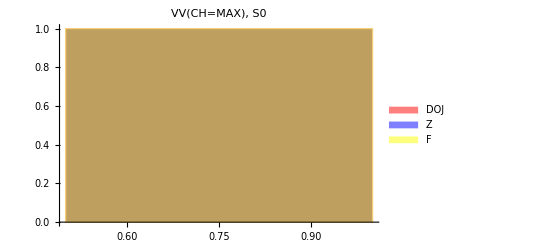
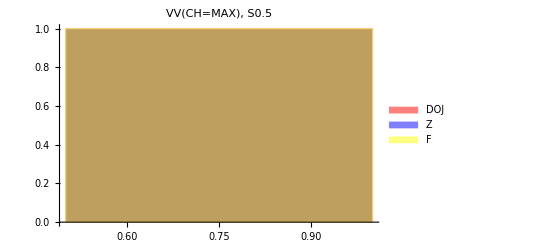
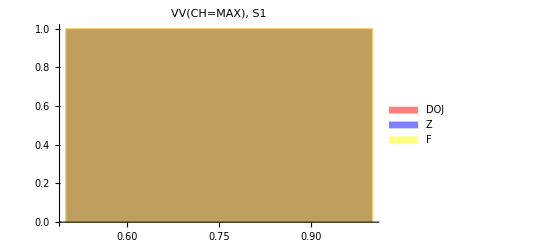
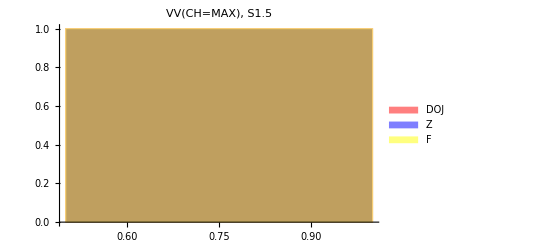
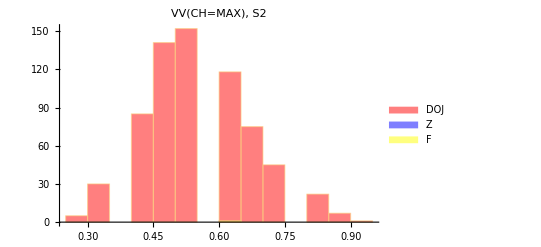
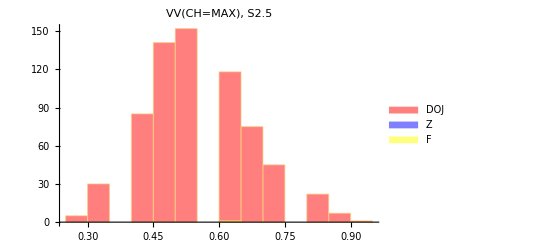
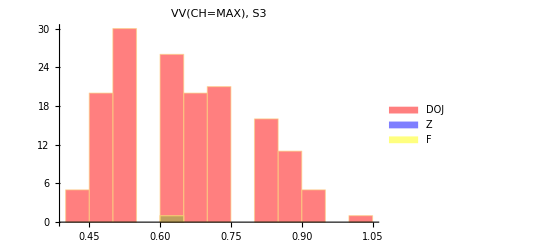
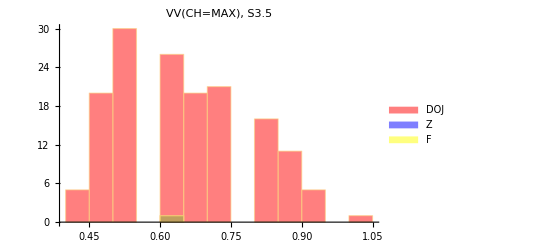
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | GrayLevel[1]

```mathematica
(*ListPlot[dojVVHist,PlotLegends->{"DOJ"},PlotStyle->{Red},PlotLabel->"VV CH=MAX geg EV&BK=DLB",PlotMarkers->{{"D",12}}, PlotRange->{0,1.05}]
ListPlot[zVVHist, PlotLegends->{"Z"},PlotStyle->{Blue},PlotLabel->"VV CH=MAX geg EV&BK=DLB",PlotMarkers->{{"Z",12}}, PlotRange->{0,1.05}]
ListPlot[fVVHist, PlotLegends->{"F"},PlotStyle->{Green},PlotLabel->"VV CH=MAX geg EV&BK=DLB",PlotMarkers->{{"F",12}}, PlotRange->{0,1.05}]
vvMaxPlot=ListPlot[{dojVVHist,zVVHist,fVVHist}, PlotLegends->{"DOJ","Z","F"},PlotStyle->{Red,Blue,Green},PlotLabel->"VV CH=MAX geg EV&BK=DLB",PlotMarkers->{{"D",12},{"Z",12},{"F",12}}, PlotRange->{0,1.05}]*)
timL={0,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7,7.5,8};
Length[timL]
hist=Map[Histogram[{dojVV[[#,2]],zVV[[#,2]],fVV[[#,2]]}, PlotLabel->"VV(CH=MAX),    S"<>ToString[timL[[#]]],ImageSize->400, ChartLegends->{"DOJ","Z","F"},ChartStyle->{Red,Blue,Yellow}]&,Range[Length[timL]]];
histOut=Grid[{hist[[1;;3]],hist[[4;;6]],hist[[7;;9]],hist[[10;;12]],hist[[13;;15]],AppendTo[hist[[16;;17]],White]},ItemSize->35]
```

```mathematica
SetDirectory["/home/carla/GDC/CH_Pool/DLB/"];
Export["COMP_DOJ_CHTAT_CHMAX_DLB.jpeg",dojPlot,ImageResolution->300]
Export["COMP_CHTAT_CHMAX_DLB.jpeg",confMAX,ImageResolution->300]
Export["VV_CHMAX_HIST_DLB.jpeg",histOut,ImageResolution->300]
Put[dojVVHist, "gdc_DOJ_VV_CHMAX_DLB.txt"]
Put[zVVHist, "gdc_Z_VV_CHMAX_DLB.txt"]
Put[fVVHist, "gdc_F_VV_CHMAX_DLB.txt"]
```

COMP_DOJ_CHTAT_CHMAX_DLB.jpeg

COMP_CHTAT_CHMAX_DLB.jpeg

VV_CHMAX_HIST_DLB.jpeg